```mathematica
A:={{1,0,-.5,-.5},{0,1,-.5,0},{0,0,1,0},{0,-.5,0,1}}
```

```mathematica
f:={.25,.25,.125,.125}
```

```mathematica
Inverse[A].f
```

Inverse[A].{0.25,0.25,0.125,0.125}

```mathematica
tri1[x_,y_]:=Boole[0<=y<=x<=1]
tri2[x_,y_]:=Boole[0≤x<=y<=1]
```

```mathematica
tri2[1.0,1]
```

1

```mathematica
f0[x_,y_]:=Piecewise[{{1-x,0<=y<=x<=1},{1-y,0≤x<=y<=1}}]
f1[x_,y_]:=Piecewise[{{y,0<=y<=x<=1},{x,0≤x<=y<=1}}]
f2[x_,y_]:=Piecewise[{{0,0<=y<=x<=1},{-x+y,0≤x<=y<=1}}]
f3[x_,y_]:=Piecewise[{{x-y,0<=y<=x<=1},{0,0≤x<=y<=1}}]
f1tri1[x_,y_]:=Piecewise[{{y,0<=y<=x<=1},{0,0≤x<=y<=1}}]
```

```mathematica
func[x_,y_]:=Sin[Pi*x]*Sin[Pi*y]
realsol[x_,y_]:=0.5*(Pi)^(-2)*Sin[Pi*x]*Sin[Pi*y]
N[func[0.5,0.5]]
```

```mathematica
f1tri1[0.4,0.5]
```

0

```mathematica
N[Integrate[Grad[f3[x,y],{x,y}].Grad[f2[x,y],{x,y}],{x,0,1},{y,0,1}]]
N[Integrate[f1tri1[x,y]*func[x,y],{x,0,1},{y,0,1}]]
N[Integrate[f1tri1[x,y],{x,0,1},{y,0,1}]]
N[func[0.785671,0.157269]]
N[f1tri1[0.785671,0.157269]]
```

0.

0.0759909

0.166667

0.29572

0.157269

```mathematica
0.05066059182116889
```

0.0506606

Plot::nonopt: Options expected (instead of {y,0,1}) beyond position 2 in Plot[func[x,y],{x,0,1},{y,0,1}]. An option must be a rule or a list of rules.

```mathematica
Plot3D[f1tri1[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[{f1tri1[x,y]*func[x,y],func[x,y]},{x,0,1},{y,0,1}]
g[x_,y_]:=Piecewise[{{x*(x-1)*y*(y-1),0<=x<=1 And 0<=y<=1}, {0,x<0 Or 1<x Or y<0 Or 1<y}}]
g0[x_,y_]:=x*(x-1)*y*(y-1)
```

-Graphics3D-

```mathematica
Plot3D[func[x,y],{x,0,1},{y,0,1}]
N[Integrate[f1tri1[x,y]*func[x,y],{x,0,1},{y,0,1}]]
```

-Graphics3D-

0.0759909

```mathematica
pde=D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==-func[x,y]
```

u^(0,2)[x,y]+u^(2,0)[x,y]==-Sin[π x] Sin[π y]

```mathematica
sol=NDSolveValue[{pde,u[0,y]==u[1,y]==u[x,0]==u[x,1]==0},u,{x,0,1},{y,0,1}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

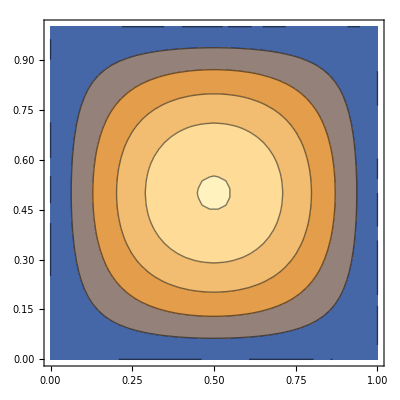

```mathematica
ContourPlot[sol[x,y],{x,0,1},{y,0,1}]
```

```mathematica
Plot3D[{sol[x,y]},{x,0,1},{y,0,1}]
Max[{realsol[x,y]}]
```

-Graphics3D-

```mathematica
0.05066059182116889 Sin[π x] Sin[π y]
N[Integrate[f1tri1[x,y]*func[x,y],{x,0,1},{y,0,1}]]
```

0.0506606 Sin[π x] Sin[π y]

0.0759909

```mathematica
results = {{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871},{0,0,0},{0,0.25,0},{0,0.5,0},{1,1,0},{0.75,1,0},{0.5,1,0},{0,1,0},{0,0.75,0},{0.25,1,0},{0.25,0,0},{0.5,0,0},{1,0,0},{1,0.25,0},{1,0.5,0},{1,0.75,0}}
```

{{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871},{0,0,0},{0,0.25,0},{0,0.5,0},{1,1,0},{0.75,1,0},{0.5,1,0},{0,1,0},{0,0.75,0},{0.25,1,0},{0.25,0,0},{0.5,0,0},{1,0,0},{1,0.25,0},{1,0.5,0},{1,0.75,0}}

```mathematica
{{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871}}
ListPlot3D[results]
```

{{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871}}

-Graphics3D-

```mathematica
ListPlot3D[{{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871},{0,0,0},{0,0.25,0},{0,0.5,0},{1,1,0},{0.75,1,0},{0.5,1,0},{0,1,0},{0,0.75,0},{0.25,1,0},{0.25,0,0},{0.5,0,0},{1,0,0},{1,0.25,0},{1,0.5,0},{1,0.75,0}}]
```